# The d=3 diamond calculation

```mathematica
dir="/Users/mb909/Documents/Academic/QFFF - Black Holes/";
yellowbroken=RGBColor[N[237/255],N[233/255],N[104/255]];
yellow=RGBColor[N[220/255],N[250/255],N[27/255]];
greyblue=RGBColor[N[45/255],N[112/255],N[140/255]];
darkgrey=RGBColor[N[30/255],N[70/255],N[87/255]];
darkblue=RGBColor[N[26/255],N[53/255],N[110/255]];
darkerblue=RGBColor[N[44/255],N[71/255],N[131/255]];
blue=RGBColor[N[66/255],N[106/255],N[181/255]];
orange=RGBColor[N[238/255],N[133/255],N[37/255]];
beamerblue=RGBColor[N[37/255],N[20/255],N[172/255]];
green=RGBColor[N[127/255],N[177/255],N[40/255]];
warmred=RGBColor[N[242/255],N[71/255],N[63/255]];
```

## Flat Diamond Plots

```mathematica
T=1;
```

```mathematica
plot1=ParametricPlot3D[{r Cos[θ],r Sin[θ],(T-r)},{r,0,3},{θ,0,2π},PlotStyle->Opacity[0.5],PlotRange->{-3,3},Mesh->None]
```

-Graphics3D-

```mathematica
θ0=0;r0=1.2;t0=1.4;
```

```mathematica
plot2=ParametricPlot3D[{r Cos[θ],r Sin[θ],t0-Sqrt[r0^2+r^2-2r0 r Sin[θ-θ0]]},{r,0,3},{θ,0,2π},PlotStyle->Opacity[0.5],Mesh->None]
```

-Graphics3D-

```mathematica
Show[plot1,plot2,AxesOrigin->{0,0,0}]
```

-Graphics3D-

## Integration limits for t=const. slices of J^+(C)∩J^-(p)

```mathematica
T=1;t0=5;x0=5;
Print[If[-(T-t0)^2+x0^2==0,"Null",If[-(T-t0)^2+x0^2<0,"Timelike","Spacelike"]]]
```

Spacelike

```mathematica
Show[Plot[T-Abs[x],{x,-T,x0+t0},PlotRange->{-x0-t0,x0+t0}],Plot[t0-Abs[x-x0],{x,-T,Max[T,t0+x0]},PlotRange->{0,Max[t0,T]}]];
Manipulate[Show[RegionPlot[{Sqrt[x^2+y^2]>T-t&&Sqrt[x^2+y^2]<T+t,Sqrt[(x-x0)^2+y^2]<t0-t},{x,-x0-t0,x0+t0},{y,-x0-t0,x0+t0},PlotStyle->Directive[Opacity[0.5],blue],Mesh->None,PlotPoints->75]],{t,0.01,t0}]
```

### Delete this:

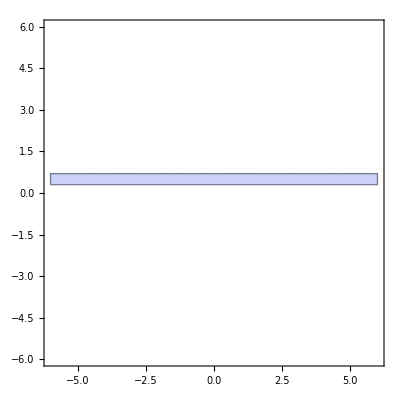

```mathematica
RegionPlot[Abs[y-(T-x0+t0)/2]<0.2,{x,-x0-t0,x0+t0},{y,-x0-t0,x0+t0}]
```

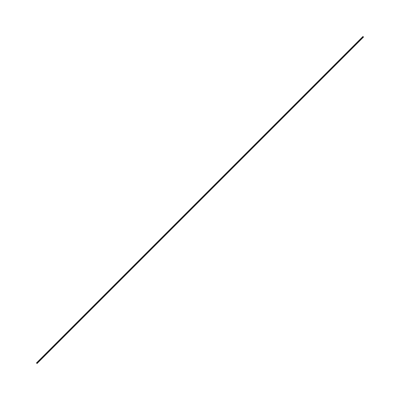

```mathematica
Graphics[Line[{{0,0},{1,1}}]]
```

```mathematica
Manipulate[Show[Graphics[Line[{{(T-x0+t0)/2,-x0-t0},{(T-x0+t0)/2,x0+t0}}]],RegionPlot[{Sqrt[x^2+y^2]>T-t&&Sqrt[x^2+y^2]<T+t,Sqrt[(x-x0)^2+y^2]<t0-t},{x,-x0-t0,x0+t0},{y,-x0-t0,x0+t0},PlotStyle->Directive[Opacity[0.5],blue],Mesh->None,PlotPoints->75]],{t,0.01,t0}]
```

```mathematica
Manipulate[
ynow=Re[-(ⅈ √((T+t0-x0) (T+t0+x0)) √((2 t+T-t0)^2-x0^2))/(2 x0)];
Show[
RegionPlot[Abs[Sqrt[x^2+y^2]-T]<t&&Sqrt[(x-x0)^2+y^2]<t0-t&&t<t0,{x,-x0-1,x0+1},{y,-x0-1,x0+1},PlotStyle->Directive[Opacity[1],blue],Mesh->None,PlotPoints->75],

RegionPlot[(x-x0)^2+y^2<(t-t0)^2,{x,-x0-1,x0+1},{y,-x0-1,x0+1},PlotStyle->Directive[Opacity[0.5],blue],Mesh->None,PlotPoints->75],

Plot[{-ynow,ynow},{x,-x0-1,x0+1}]],
{t,0,t0}(*,AnimationRate->0.1*)]
```

```mathematica
t0=.;T=.;t0=.;t=.;x0=.
```

```mathematica
Solve[t==T-Sqrt[x^2+y^2]&&t==t0-Sqrt[(x-x0)^2+y^2],{x,y}]//FullSimplify
```

{{x→((T-t0) (-2 t+T+t0)+x0^2)/(2 x0),y→-(ⅈ √((T-t0)^2-x0^2) √((-2 t+T+t0)^2-x0^2))/(2 x0)},{x→((T-t0) (-2 t+T+t0)+x0^2)/(2 x0),y→(ⅈ √((T-t0)^2-x0^2) √((-2 t+T+t0)^2-x0^2))/(2 x0)}}

```mathematica
Integrate[1,{
```

```mathematica
t0=1;T=1;x0=1.5;t=0.3
```

0.3

```mathematica
√((-2 t+T+t0)^2-x0^2)
```

0.+0.538516 ⅈ

```mathematica
√((2 t+T-t0)^2-x0^2)
```

0.+1.37477 ⅈ

```mathematica
(ⅈ √((T+t0-x0) (T+t0+x0)) √((2 t+T-t0)^2-x0^2))/(2 x0)
```

-0.606218+0. ⅈ

```mathematica
......
```

```mathematica
Show[RegionPlot3D[Abs[Sqrt[x^2+y^2]-T]<t&&Sqrt[(x-x0)^2+y^2]<t0-t&&t<t0&&t=0.25,{x,-2,2},{y,-2,2},{t,-0.1,2},PlotStyle->Opacity[0.5],Mesh->None,Boxed->False,AxesOrigin->{0,0,0},PlotPoints->50],Plot3D[0.25,{x,-2,2},{y,-2,2}]]
```

-Graphics3D-

```mathematica
$Assumptions={T,t,x,y,t0,x0}∈Reals&&T>0&&t>0&&t0>0;
```

```mathematica
T=.;x0=.;t0=.
```

```mathematica
Reduce[Sqrt[x^2+y^2]-T<t^2&&Sqrt[(x-x0)^2+y^2]<t0-t]
```

(t|x0)∈Reals&&T>-t^2&&-t^2-T<x<t^2+T&&((-√(t^4+2 t^2 T+T^2-x^2)<y<0&&t0>t+√(x^2-2 x x0+x0^2+y^2))||(y==0&&((x0<x&&t0>t+√(x^2-2 x x0+x0^2))||(x0==x&&t0>t-√(x^2-2 x x0+x0^2))||(x0>x&&t0>t+√(x^2-2 x x0+x0^2))))||(0<y<√(t^4+2 t^2 T+T^2-x^2)&&t0>t+√(x^2-2 x x0+x0^2+y^2)))

```mathematica
FindMinimum[{y,y^2+x^2>3},{y,}]
```

FindMinimum[{y,y^2+x^2>3},y]

```mathematica
FindMinimum[{x Cos[x],1≤x≤15},{x,7}]
```

{-9.47729,{x→9.52933}}

```mathematica
T=1;
```

```mathematica
ParametricPlot3D[{{x,y,-Sqrt[x^2+y^2]+T},{x,y,+Sqrt[x^2+y^2]-T}},{x,-2,2},{y,-2,2},PlotRange->{{-2,2},{-2,2},{0,2}}]
```

-Graphics3D-

```mathematica
T=1;t=0.3;
```

```mathematica
Plot[x==3,{x,-2,2},{y,-2,2}]
```

Plot[x==3,{x,-2,2},{y,-2,2}]

```mathematica
ArcSin[-1]
```

-π/2

```mathematica
Integrate[Cos[θ]^2,θ]
```

θ/2+1/4 Sin[2 θ]

```mathematica
$Assumptions=d>0&&R>0&&r>0;
```

```mathematica
int1=Integrate[2Sqrt[r^2-(x-d)^2],x]
```

((d-x) (d^2-r^2-2 d x+x^2)+r^2 √(-d^2+r^2+2 d x-x^2) ArcTan[(-d+x)/(√(r^2-(d-x)^2))])/(√(-d^2+r^2+2 d x-x^2))

```mathematica
int1upper=int1/.{x->(R^2-r^2+d^2)/(2d)}//FullSimplify
```

(((d-r-R) (d+r-R) (d-r+R) (d+r+R) (d^2+r^2-R^2))/(8 d^3)-r^2 √(R^2-((d^2-r^2+R^2)^2)/(4 d^2)) ArcTan[(d^2+r^2-R^2)/(√(-(d-r-R) (d+r-R) (d-r+R) (d+r+R)))])/(√(R^2-((d^2-r^2+R^2)^2)/(4 d^2)))

```mathematica
int1
```

((d-x) (d^2-r^2-2 d x+x^2)+r^2 √(-d^2+r^2+2 d x-x^2) ArcTan[(-d+x)/(√(r^2-(d-x)^2))])/(√(-d^2+r^2+2 d x-x^2))

```mathematica
int1lower=Limit[int1,x->d-r]//FullSimplify
```

-(π r^2)/2

```mathematica
int1upper-int1lower//FullSimplify
```

(√(-((d-r-R) (d+r-R) (d-r+R) (d+r+R))/d^2) (-r^2+R^2)-d (-2 π r^2+√(-(d-r-R) (d+r-R) (d-r+R) (d+r+R))))/(4 d)-r^2 ArcTan[(d^2+r^2-R^2)/(√(-(d-r-R) (d+r-R) (d-r+R) (d+r+R)))]

```mathematica
int1lower=int1/.{x->
```

```mathematica
2Integrate[1/2 (x √(r^2-x^2)+r^2 ArcTan[x/(√(r^2-x^2))])
```

```mathematica
FullSimplify[Cos[ArcSin[x]]]
```

√(1-x^2)

```mathematica
Integrate[Sqrt[1-x^2],x]
```

1/2 (x √(1-x^2)+ArcSin[x])

```mathematica
NIntegrate[Boole[Abs[Sqrt[x^2+y^2]-T]<t&&Sqrt[(x-x0)^2+y^2]<t0-t],{x,-3,3},{y,-3,3}]//Chop
```

0.987373

## Area of the intersection of two circles:

```mathematica
circle1=x^2+y^2<R^2;circle2=(x-d)^2+y^2<r^2;
```

### Values:

```mathematica
d=4;R=3;r=3;
circle1=x^2+y^2<R^2;circle2=(x-d)^2+y^2<r^2;
xs=(R^2-r^2+d^2)/(2d);
A=π/2(R^2+r^2)+r^2 ArcSin[(xs-d)/r]-R^2 ArcSin[xs/R]+(xs-d)Sqrt[r^2-(xs-d)^2]-xs Sqrt[R^2-xs^2]//FullSimplify;
```

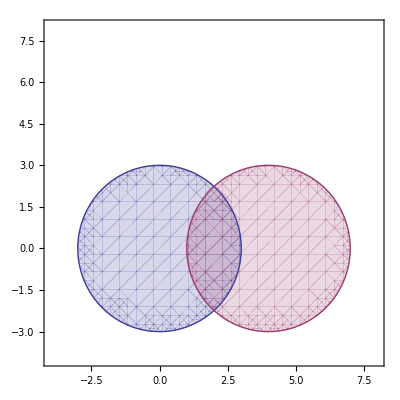

```mathematica
RegionPlot[{circle1,circle2},{x,Min[-R,d-r]-1,Max[R,r+d]+1},{y,Min[-R,d-r]-1,Max[R,r+d]+1},AspectRatio->1]
```

```mathematica
NIntegrate[Boole[circle1&&circle2],{x,Min[-R,d-r]-1,Max[R,r+d]+1},{y,Min[-R,d-r]-1,Max[R,r+d]+1}]
```

6.19496

```mathematica
A//N
```

6.19496

```mathematica
d=.;r=.;R=.;xs=(R^2-r^2+d^2)/(2d);
```

```mathematica
π/2(R^2+r^2)+r^2 ArcSin[(xs-d)/r]-R^2 ArcSin[xs/R]+(xs-d)Sqrt[r^2-(xs-d)^2]-xs Sqrt[R^2-xs^2]//FullSimplify
```

-d √(R^2-((d^2-r^2+R^2)^2)/(4 d^2))+r^2 ArcSec[(2 d r)/(d^2+r^2-R^2)]+R^2 ArcSec[(2 d R)/(d^2-r^2+R^2)]

```mathematica
Sqrt[r^2-(xs-d)^2]//FullSimplify
```

√(r^2-((d^2+r^2-R^2)^2)/(4 d^2))

```mathematica
Sqrt[R^2-xs^2]//FullSimplify
```

√(R^2-((d^2-r^2+R^2)^2)/(4 d^2))

```mathematica
(xs-d)Sqrt[r^2-(xs-d)^2]-xs Sqrt[R^2-xs^2]//FullSimplify
```

-d √(R^2-((d^2-r^2+R^2)^2)/(4 d^2))

```mathematica
t=.;t0=.;x0=.;T=.
```

```mathematica
$Assumptions=t0>0&&x0>0&&t0>0&&T>0;
```

```mathematica
d=.;R=.;r=.;
```

```mathematica
integrand1=-d √(R^2-((d^2-r^2+R^2)^2)/(4 d^2))+r^2 ArcSec[(2 d r)/(d^2+r^2-R^2)]+R^2 ArcSec[(2 d R)/(d^2-r^2+R^2)]/.{d->x0,r->t0-t,R->t+T}//FullSimplify
```

-1/2 √(-(T+t0-x0) (T+t0+x0) ((2 t+T-t0)^2-x0^2))+(t-t0)^2 ArcSec[(2 (-t+t0) x0)/(-(2 t+T-t0) (T+t0)+x0^2)]+(t+T)^2 ArcSec[(2 (t+T) x0)/((2 t+T-t0) (T+t0)+x0^2)]

```mathematica
integrand2=-d √(R^2-((d^2-r^2+R^2)^2)/(4 d^2))+r^2 ArcSec[(2 d r)/(d^2+r^2-R^2)]+R^2 ArcSec[(2 d R)/(d^2-r^2+R^2)]/.{d->x0,r->t0-t,R->T-t}//FullSimplify
```

-1/2 √(-((T-t0)^2-x0^2) ((-2 t+T+t0)^2-x0^2))+(t-t0)^2 ArcSec[(2 (t-t0) x0)/((T-t0) (-2 t+T+t0)-x0^2)]+(t-T)^2 ArcSec[(2 (-t+T) x0)/((T-t0) (-2 t+T+t0)+x0^2)]

```mathematica
integrand=integrand1-integrand2//FullSimplify
```

1/2 (-√(-(T+t0-x0) (T+t0+x0) ((2 t+T-t0)^2-x0^2))+√(-((T-t0)^2-x0^2) ((-2 t+T+t0)^2-x0^2)))-(t-t0)^2 ArcSec[(2 (t-t0) x0)/((T-t0) (-2 t+T+t0)-x0^2)]+(t-t0)^2 ArcSec[(2 (-t+t0) x0)/(-(2 t+T-t0) (T+t0)+x0^2)]+(t+T)^2 ArcSec[(2 (t+T) x0)/((2 t+T-t0) (T+t0)+x0^2)]-(t-T)^2 ArcSec[(2 (-t+T) x0)/((T-t0) (-2 t+T+t0)+x0^2)]

```mathematica
int=Integrate[integrand,t]
```

(-(t^2 x0)/24-1/48 T (5 T+3 t0) x0-1/48 t (7 T+3 t0) x0) √(-((4 t^2+4 t T+T^2-4 t t0-2 T t0+t0^2-x0^2) (T^2+2 T t0+t0^2-x0^2))/((t+T)^2 x0^2))-1/8 (-2 t+T+t0) √(-(T^2-2 T t0+t0^2-x0^2) ((-2 t+T+t0)^2-x0^2))+1/4 (-T+1/2 (-2 t+T+t0)) √(-(T^2+2 T t0+t0^2-x0^2) (4 T^2-4 T (-2 t+T+t0)+(-2 t+T+t0)^2-x0^2))+(1/24 (t-t0)^2 x0-1/16 (t-t0) (T+t0) x0) √(((T^2+4 T (t-t0)+4 (t-t0)^2+2 T t0+4 (t-t0) t0+t0^2-x0^2) (-T^2-2 T t0-t0^2+x0^2))/((t-t0)^2 x0^2))-(1/24 (t-T)^2 x0-1/16 (t-T) (T-t0) x0) √(((4 (t-T)^2+4 (t-T) T+T^2-4 (t-T) t0-2 T t0+t0^2-x0^2) (-T^2+2 T t0-t0^2+x0^2))/((t-T)^2 x0^2))-(1/24 (t-t0)^2 x0+1/16 (t-t0) (T-t0) x0) √(((T^2-4 T (t-t0)+4 (t-t0)^2-2 T t0+4 (t-t0) t0+t0^2-x0^2) (-T^2+2 T t0-t0^2+x0^2))/((t-t0)^2 x0^2))-1/3 (t-t0)^3 ArcSec[(2 (t-t0) x0)/((T-t0) (-2 t+T+t0)-x0^2)]+1/3 (t-t0)^3 ArcSec[-(2 (t-t0) x0)/(-(2 t+T-t0) (T+t0)+x0^2)]+1/3 t (t^2+3 t T+3 T^2) ArcSec[(2 (t+T) x0)/((2 t+T-t0) (T+t0)+x0^2)]-1/3 (t-T)^3 ArcSec[-(2 (t-T) x0)/((T-t0) (-2 t+T+t0)+x0^2)]-1/3 T^3 ArcSin[(2 t T+T^2+2 t t0-t0^2+x0^2)/(2 (t+T) x0)]+(ⅈ x0^2 (-T^2+2 T t0-t0^2+x0^2) Log[-2 ⅈ (-2 t+T+t0) √(T^2-2 T t0+t0^2-x0^2)+2 √(-(T^2-2 T t0+t0^2-x0^2) ((-2 t+T+t0)^2-x0^2))])/(8 √(T^2-2 T t0+t0^2-x0^2))+1/48 √(-T^2-2 T t0-t0^2+x0^2) (2 T^2+4 T t0+2 t0^2+x0^2) Log[-T^3-2 T^2 (t-t0)-3 T^2 t0-4 T (t-t0) t0-3 T t0^2-2 (t-t0) t0^2-t0^3+T x0^2+2 (t-t0) x0^2+t0 x0^2+(t-t0) x0 √(-T^2-2 T t0-t0^2+x0^2) √(((T^2+4 T (t-t0)+4 (t-t0)^2+2 T t0+4 (t-t0) t0+t0^2-x0^2) (-T^2-2 T t0-t0^2+x0^2))/((t-t0)^2 x0^2))]-1/48 √(-T^2+2 T t0-t0^2+x0^2) (2 T^2-4 T t0+2 t0^2+x0^2) Log[-2 (t-T) T^2-T^3+4 (t-T) T t0+3 T^2 t0-2 (t-T) t0^2-3 T t0^2+t0^3+2 (t-T) x0^2+T x0^2-t0 x0^2+(t-T) x0 √(-T^2+2 T t0-t0^2+x0^2) √(((4 (t-T)^2+4 (t-T) T+T^2-4 (t-T) t0-2 T t0+t0^2-x0^2) (-T^2+2 T t0-t0^2+x0^2))/((t-T)^2 x0^2))]-1/48 √(-T^2+2 T t0-t0^2+x0^2) (2 T^2-4 T t0+2 t0^2+x0^2) Log[T^3-2 T^2 (t-t0)-3 T^2 t0+4 T (t-t0) t0+3 T t0^2-2 (t-t0) t0^2-t0^3-T x0^2+2 (t-t0) x0^2+t0 x0^2+(t-t0) x0 √(-T^2+2 T t0-t0^2+x0^2) √(((T^2-4 T (t-t0)+4 (t-t0)^2-2 T t0+4 (t-t0) t0+t0^2-x0^2) (-T^2+2 T t0-t0^2+x0^2))/((t-t0)^2 x0^2))]+1/(48 √(T^2+2 T t0+t0^2-x0^2))ⅈ (2 T^4+8 T^3 t0+12 T^2 t0^2+8 T t0^3+2 t0^4-T^2 x0^2-2 T t0 x0^2-t0^2 x0^2-x0^4) Log[2 (t+T) x0 √(-((4 t^2+4 t T+T^2-4 t t0-2 T t0+t0^2-x0^2) (T^2+2 T t0+t0^2-x0^2))/((t+T)^2 x0^2))-(2 ⅈ (2 t T^2+T^3+4 t T t0+T^2 t0+2 t t0^2-T t0^2-t0^3-2 t x0^2-T x0^2+t0 x0^2))/(√(T^2+2 T t0+t0^2-x0^2))]+1/8 ⅈ x0^2 √(T^2+2 T t0+t0^2-x0^2) Log[2 √(-(T^2+2 T t0+t0^2-x0^2) (4 T^2-4 T (-2 t+T+t0)+(-2 t+T+t0)^2-x0^2))+(2 ⅈ (2 T^3+4 T^2 t0+2 T t0^2-T^2 (-2 t+T+t0)-2 T t0 (-2 t+T+t0)-t0^2 (-2 t+T+t0)-2 T x0^2+(-2 t+T+t0) x0^2))/(√(T^2+2 T t0+t0^2-x0^2))]

```mathematica
integral1=int/.{t->0}//Simplify
```

1/48 ((3 T-5 t0) √(-(T^2-2 T t0+t0^2-x0^2) ((T+t0)^2-x0^2))-6 (T-t0) √(-(T^2-2 T t0+t0^2-x0^2) ((T+t0)^2-x0^2))-6 (T+t0) √(-(T^2-2 T t0+t0^2-x0^2) ((T+t0)^2-x0^2))+(-5 T+3 t0) √(-(T^2-2 T t0+t0^2-x0^2) ((T+t0)^2-x0^2))-(5 T+3 t0) √(-(T^2-2 T t0+t0^2-x0^2) ((T+t0)^2-x0^2))+(3 T+5 t0) √(-(T^2-2 T t0+t0^2-x0^2) ((T+t0)^2-x0^2))+16 T^3 ArcSec[(2 T x0)/(T^2-t0^2+x0^2)]-16 T^3 ArcSin[(T^2-t0^2+x0^2)/(2 T x0)]+(ⅈ (2 T^4+8 T^3 t0+2 t0^4-t0^2 x0^2-x0^4+T^2 (12 t0^2-x0^2)+T (8 t0^3-2 t0 x0^2)) Log[-2 ⅈ (T-t0) √(T^2+2 T t0+t0^2-x0^2)+2 √(-(T^2-2 T t0+t0^2-x0^2) (T^2+2 T t0+t0^2-x0^2))])/(√(T^2+2 T t0+t0^2-x0^2))-6 ⅈ x0^2 √(T^2-2 T t0+t0^2-x0^2) Log[-2 ⅈ (T+t0) √(T^2-2 T t0+t0^2-x0^2)+2 √(-(T^2-2 T t0+t0^2-x0^2) ((T+t0)^2-x0^2))]+6 ⅈ x0^2 √(T^2+2 T t0+t0^2-x0^2) Log[(2 ⅈ T^3+2 ⅈ T^2 t0-2 ⅈ t0^3+2 ⅈ t0 x0^2-2 ⅈ T (t0^2+x0^2)+2 √(T^2+2 T t0+t0^2-x0^2) √(-T^4-(t0^2-x0^2)^2+2 T^2 (t0^2+x0^2)))/(√(T^2+2 T t0+t0^2-x0^2))]+√(-T^2-2 T t0-t0^2+x0^2) (2 T^2+4 T t0+2 t0^2+x0^2) Log[-T^3-T^2 t0+t0^3-t0 x0^2+T (t0^2+x0^2)-√(-T^2-2 T t0-t0^2+x0^2) √(-T^4-(t0^2-x0^2)^2+2 T^2 (t0^2+x0^2))]-2 √(-T^2+2 T t0-t0^2+x0^2) (2 T^2-4 T t0+2 t0^2+x0^2) Log[T^3-T^2 t0+t0^3-t0 x0^2-T (t0^2+x0^2)-√(-T^2+2 T t0-t0^2+x0^2) √(-T^4-(t0^2-x0^2)^2+2 T^2 (t0^2+x0^2))])

```mathematica
integral2=int/.{t->(T-x0+t0)/2}//Simplify
```

1/48 (-12 (2 T-x0) √(-T (T-x0) (T^2+2 T t0+t0^2-x0^2))-2 x0 √(-(T (T-x0) (T^2+2 T t0+t0^2-x0^2))/((3 T+t0-x0)^2 x0^2)) (18 T^2+18 T t0+4 t0^2-9 T x0-5 t0 x0+x0^2)+2 x0 √(-(T (T-x0) (T^2+2 T t0+t0^2-x0^2))/(x0^2 (-T+t0+x0)^2)) (-2 T^2+4 t0^2+5 t0 x0+x0^2+T (-2 t0+x0))+2 (19 T^2+8 T (t0-x0)+(t0-x0)^2) (T+t0-x0) ArcSec[((3 T+t0-x0) x0)/((T+t0) (2 T-x0)+x0^2)]-2 (-T+t0+x0)^3 ArcSec[(x0 (-T+t0+x0))/(-2 T^2+T (-2 t0+x0)+x0 (t0+x0))]-16 T^3 ArcSin[(2 T^2+2 T t0-T x0-t0 x0+x0^2)/((3 T+t0-x0) x0)]-6 ⅈ x0^2 √(T^2-2 T t0+t0^2-x0^2) Log[-2 ⅈ x0 √(T^2-2 T t0+t0^2-x0^2)]-2 √(-T^2+2 T t0-t0^2+x0^2) (2 T^2-4 T t0+2 t0^2+x0^2) Log[x0 (T^2-2 T t0+t0^2-x0^2)]+6 ⅈ x0^2 √(T^2+2 T t0+t0^2-x0^2) Log[2 (ⅈ (2 T-x0) √(T^2+2 T t0+t0^2-x0^2)+2 √(-T (T-x0) (T^2+2 T t0+t0^2-x0^2)))]+(ⅈ (2 T^4+8 T^3 t0+2 t0^4-t0^2 x0^2-x0^4+T^2 (12 t0^2-x0^2)+T (8 t0^3-2 t0 x0^2)) Log[2 (-ⅈ (2 T-x0) √(T^2+2 T t0+t0^2-x0^2)+2 (3 T+t0-x0) x0 √(-(T (T-x0) (T^2+2 T t0+t0^2-x0^2))/((3 T+t0-x0)^2 x0^2)))])/(√(T^2+2 T t0+t0^2-x0^2))+√(-T^2-2 T t0-t0^2+x0^2) (2 T^2+4 T t0+2 t0^2+x0^2) Log[(2 √(-T^2-2 T t0-t0^2+x0^2) (T^(3/2) √(-(T-x0) (T^2+2 T t0+t0^2-x0^2))-(t0+x0) √(T (-T+x0) (T^2+2 T t0+t0^2-x0^2)))-(2 T-x0) (T^2+2 T t0+t0^2-x0^2) Abs[-T+t0+x0])/Abs[-T+t0+x0]])

```mathematica
integral2-integral1//FullSimplify
```

$Aborted